```mathematica
deq=D[Y[x,t],t]-𝒟 D[Y[x,t],{x,2}]==0
```

Y^(0,1)[x,t]-𝒟 Y^(2,0)[x,t]==0

```mathematica
f0[t_]:=0.5
```

```mathematica
f1[t_]:=0.5
```

```mathematica
g0[x_]:=1/2(1+Sin[π x])
```

```mathematica
sol=DSolve[{
deq,
Y[0,t]==f0[t],
Y[1,t]==f1[t],
Y[x,0]==g0[x]},
Y[x,t],{x,t}]
```

{{Y[x,t]→1/2+1/2 ⅇ^(-π^2 t 𝒟) Sin[π x]}}

```mathematica
Yf[x_,t_]:=Y[x,t]/.sol[[1]]
```

```mathematica
Yf[x_,t_]:=1/2(1+ⅇ^(-π^2 𝒟 t)Sin[π x])
```

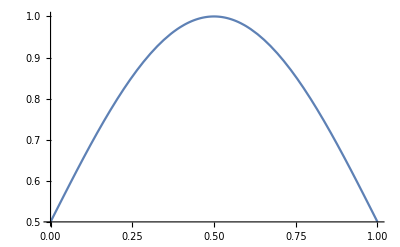

```mathematica
Plot[g0[x],{x,0,1}]
```

```mathematica
𝒟=1;
```

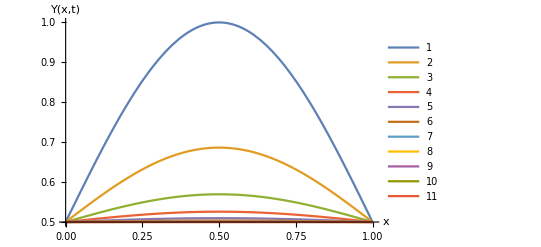

```mathematica
Plot[{Yf[x,0],Yf[x,0.1],Yf[x,0.2],Yf[x,0.3],Yf[x,0.4],Yf[x,0.5],Yf[x,0.6],Yf[x,0.7],Yf[x,0.8],Yf[x,0.9],Yf[x,1]},{x,0,1},AxesLabel->{"x","Y(x,t)"},PlotRange->All,PlotLegends->Automatic]
```